```mathematica
SetDirectory[DirectoryName[ToFileName["FileName"/.NotebookInformation[SelectedNotebook[]]]]]
```

C:\Users\Simone\Dropbox\Magistrale\1Anno\2Semestre\MC\Progetto Passaretti Cimmino Cappella\Progetto Passaretti Cimmino Cappella

```mathematica
<<Progetto.m
```

# Trigonometria

La trigonometria è la parte della matematica che studia i triangoli a partire dai loro angoli. 

Il compito principale della trigonometria, consiste nel calcolare le misure che caratterizzano gli elementi di un triangolo (lati, angoli, mediane, etc...) partendo da altre misure già note per mezzo di speciali funzioni. 

Tali funzioni sono le funzioni trigonometriche: queste si differenziano in funzioni trigonometriche dirette e indirette:

- Sono dette  dirette quelle che ad un angolo, solitamente espresso in radianti, associano una lunghezza o un rapporto fra lunghezze. 

A causa dell’equivalenza circolare degli angoli, tutte le funzioni trigonometriche dirette sono anche funzioni periodiche con periodo π o 2π.

	- Seno      
	- Coseno
	- Tangente
	
-  Sono dette indirette le funzioni inverse associate a quelle dirette. 

Il dominio di ciascuna funzione trigonometrica inversa corrisponde al codominio della rispettiva funzione diretta. 

Queste sono Arcoseno, Arcocoseno, Arcotangente.

# Definizioni di Seno, Coseno e Tangente

Dato un angolo α, riferiamolo a un sistema di assi cartesiani ortogonali in modo che si trovi in posizione normale e tracciamo la circonferenza unitaria (raggio 1). 

Il seno, il coseno e la tangente di α sono definiti come:
	
- Seno: il rapporto fra il cateto opposto all’angolo e l’ipotenusa del triangolo OAB. 
In simboli:

	sin(α)=AB/OB
	
Avendo tuttavia scelto una circonferenza goniometrica di raggio 1, si ha che:

	sin(α)=AB

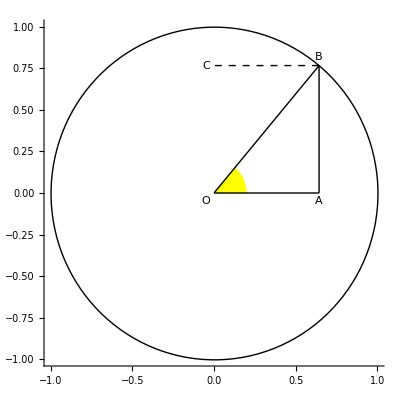

```mathematica
DrawSinStat[]
```

- Coseno: ragionamento analogo può essere effettuato per il coseno, definito come il rapporto fra il cateto adiacente all'angolo e l'ipotenusa del triangolo OAB.

In simboli:

	cos(α)=OA/OB
	
Essendo il cerchio di raggio 1 analogamente:

	cos(α)=OA

```mathematica
DrawCosStat[]
```

-Graphics-

- Tangente: ricordando sempre che la circonferenza goniometrica considerata ha raggio unitario, posiamo affermare che OB è uguale a OD che è uguale a 1, rappresentando entrambe il raggio della circonferenza. 

Ora concentriamoci sui triangoli OAB e ODE; questi sono triangoli simili. 
Nell’immagine sottostante è mosrato un esempio di triangoli simili:

```mathematica
LoadImage["images.jpg"]
```

-Graphics-

I due triangoli OAB e ODE hanno tutti e tre gli angoli della stessa ampiezza:

	- angolo α in comune,
	- entrambi sono triangoli rettangoli
	- la somma degli angoli interni di un triangolo è 180°, dunque anche l'angolo restante è della 	stessa dimensione

In particolare i lati di triangoli simili sono ordinatamente in proporzione, quindi vale la relazione seguente:

	DE / OD = AB / OA

Ricordando che la circonferenza ha raggio unitario e che la lunghezza del segmento DE è proprio la tangente dell'angolo, si ha:

tan(α) = AB / OA

ossia

tan(α) = sin(α) / cos(α)

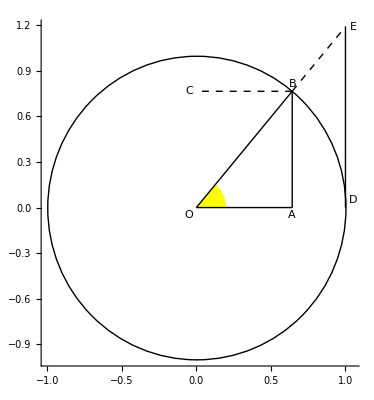

```mathematica
DrawTanStat[]
```

Di seguito è possibile osservare una rappresentazione di tutte le funzioni precedentemente definite.

```mathematica
DrawSinCosStat[]
```

-Graphics-

Nel grafico successivo è possibile modificare l’ampiezza dell’angolo α tra 0 e 2π in maniera tale da capire come cambia il valore di seno, coseno e tangente in funzione dell’ampiezza dell’angolo:

```mathematica
DrawSinCosDyn[]
```

Nell’animazione sono mostrate le rappresentazioni dei valori del seno, coseno e tangente in funzione dell’angolo α, che varia tra 0 e 2π. 

COSA ACCADE IN FIGURA?

Primo quadrante
In particolare a partire dalla posizione iniziale del grafico, per un valore di α pari a 0, si evince come il seno assuma valore 1, pari al raggio del cerchio unitario, mentre il coseno e la tangente siano nulli. 

Aumentando quindi ora il valore dell’angolo, vediamo come il seno diminuisce e al contempo il coseno aumenta assieme al valore della tangente, fino a raggiungere l’ampiezza di π/2 dove il valore del seno si annulla, quello del coseno è uguale a 1 e la tangente assume valore ∞ . 

Secondo Quadrante
Superata tale ampiezza il seno inizia ad assumere un valore negativo, trovandosi ora nel semipiano negativo delle ascisse. 

Man mano che l’angolo aumenta, e ci si avvicina all’ampiezza di π, il coseno si avvicina sempre più a un valore nullo, come per la tangente, e il seno diminuisce fino a raggiungere il valore -1. 

Terzo Quadrante
Ora raggiunto quindi il terzo quadrante, dove le coordinate sono entrambe negative, il valore di seno, coseno e della tangente saranno tutti minori di 0, in particolare raggiunta l’ampiezza di 3/2 π, il seno si annulla, il coseno raggiunge il valore -1 e la tangente -∞. 

Quarto quadrante
A questo punto raggiunto quindi il quarto quadrante, i valori del seno e del coseno e tangente man mano che ci si avvicina all’ampiezza dell’angolo 2π, assumono di nuovo i valori iniziali. 

Da ciò si può dedurre come seno e coseno siano funzioni periodiche di periodo 2π mentre la tangente di periodo π; entrambi i periodi sono centrati in 0.

# Periodicità

Come detto nel paragrafo precedente, le funzioni seno, coseno e tangente sono periodiche. 

Ciò vuol dire che, nel caso del seno e del coseno, ogni qualvolta si compie un giro completo del cerchio raggiungendo il valore di ampiezza dell’angolo pari a 2π il valore delle due funzioni torna a essere lo stesso dell’angolo pari a 0. 

Ciò vuol dire che per valori dell’angolo pari a 2k volte π, il valore delle due sarà sempre lo stesso. 

Ciò vale anche per la tangente con la sola differenza che il valore della funzione si ripete con periodo pari a k volte π.

```mathematica
DrawPeriodicSin[]
```

Nel grafico precedente viene mostrata la periodicità del seno, mettendo in relazione il suo valore con l’andamento della sua funzione che viene illustrata nell’intervallo [0, 4π].

All’aumentare del valore dell’ampiezza dell’angolo, il valore della funzione oscilla tra -1 e 1 (dominio della funzione).

Nel grafico a destra, il punto che si muove lungo la sinusoide mostra il valore corrente del seno corrispondente al suo valore nella circonferenza unitaria.

```mathematica
DrawPeriodicCos[]
```

Allo stesso modo anche per il coseno, viene messo in relazione il suo valore con l’andamento della sua funzione che viene illustrata nell’intervallo [0, 4π].

All’aumentare del valore dell’ampiezza dell’angolo, il valore della funzione oscilla tra -1 e 1 (dominio della funzione).

Nel grafico a destra, il punto che si muove lungo la cosinusoide mostra il valore corrente del coseno corrispondente al suo valore nella circonferenza unitaria.

```mathematica
DrawPeriodicTan[]
```

Infine, per quanto riguarda la tangente, viene messo in relazione il suo valore con l’andamento della sua funzione che viene illustrata nell’intervallo [0, 4π].

All’aumentare dell’ampiezza dell’angolo, il valore della funzione oscilla tra -∞ e ∞ (dominio della funzione).
Nel grafico a destra, il punto che si muove lungo la tangentoide mostra il valore corrente del coseno corrispondente al suo valore nella circonferenza unitaria.

# Riepilogo

Di seguito è mostrato un riepilogo delle tre funzioni mettendo in relazione valore e andamento della funzione.

Clicca sul pulsante Funzione per cambiare scenario.

```mathematica
Riepilogo[]
```

# Bibliografia

1 - https://it.wikipedia.org/wiki/Trigonometria

2 - http://www.youmath.it/formulari/65-formulari-di-trigonometria-logaritmi-esponenziali.html

3 - http://www.youmath.it/lezioni/analisi-matematica/le-funzioni-elementari-e-le-loro-proprieta/144-seno-e-coseno-di-un-angolo.html

# Chi siamo

```mathematica
LoadImage["simone.jpg"]
```

-Graphics-

Passaretti Simone

```mathematica
LoadImage["martin.jpg"]
```

-Graphics-

Martin Cimmino

```mathematica
LoadImage["matteo.jpg"]
```

-Graphics-

Matteo Cappella